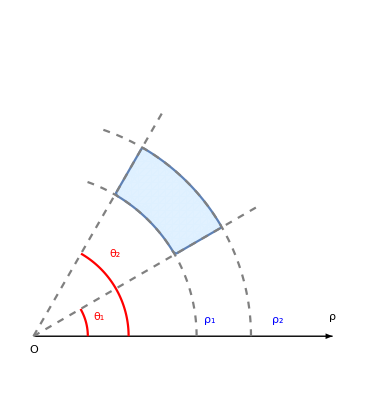

```mathematica
(********坐标轴*******)
f1={
Graphics[{{Black,Arrowheads[0.03],Arrow[{{0,0},{1.1,0}}]},
{White,Arrowheads[0.03],Arrow[{{0,-0.1},{0,1.1}}]}}],
Graphics[{Text[Style[ρ,Large],{1.1,0.07}],
Text[Style[O,Large,Italic],{0,-0.05}]
}]
};
(*********阴影区域*********)
f2={
RegionPlot[0.36<x^2+y^2<0.64&&1/Sqrt[3]<y/x<Sqrt[3],
{x,0,1},{y,0,1},
PlotStyle->Directive[LightBlue,Opacity[0.9]],
PlotPoints->40
]
};
(********边界线*******)
f3={
PolarPlot[{0.6,0.8},{t,0,2*Pi/5},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}],
ParametricPlot[{{t/2,t*Sqrt[3]/2},{t*Sqrt[3]/2,t/2}},{t,0,0.95},
PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]
};
(*********辅助线、点*********)
f4={
PolarPlot[{0.2},{t,0,Pi/6},PlotStyle->{Red}],
PolarPlot[{0.35},{t,0,Pi/3},PlotStyle->{Red}]
};
(*********文字标记*********)
f5={
Graphics[
{
Text[Style["θ_1",Large,Red],{0.24,0.07}],
Text[Style["θ_2",Large,Red],{0.3,0.3}],
Text[Style["ρ_1",Large,Blue],{0.65,0.06}],
Text[Style["ρ_2",Large,Blue],{0.9,0.06}]
}
]
};
(*********选择显示*********)
Show[f1,f2,f3,f4,f5]
```

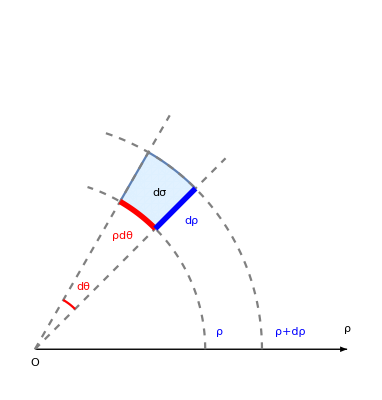

```mathematica
(********坐标轴*******)
f1={
Graphics[{
{Black,Arrowheads[0.03],Arrow[{{0,0},{1.1,0}}]},
{White,Arrowheads[0.03],Arrow[{{0,0},{0,1.1}}]}
}],
Graphics[{Text[Style[ρ,Large],{1.1,0.07}],
Text[Style[O,Large,Italic],{0,-0.05}]
}]
};
(*********阴影区域*********)
f2={
RegionPlot[0.36<x^2+y^2<0.64&&1<y/x<Sqrt[3],
{x,0,1},{y,0,1},
PlotStyle->Directive[LightBlue,Opacity[0.9]],
PlotPoints->40
]
};
(********边界线*******)
f3={
PolarPlot[{0.6,0.8},{t,0,2*Pi/5},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}],
ParametricPlot[{{t/2,t*Sqrt[3]/2},{t*Sqrt[2]/2,t*Sqrt[2]/2}},{t,0,0.95},
PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]
};
(*********辅助线、点*********)
f4={
PolarPlot[{0.2},{t,Pi/4,Pi/3},PlotStyle->{Red}],
PolarPlot[{0.6},{t,Pi/4,Pi/3},PlotStyle->{Red,Thickness[0.01]}],
ParametricPlot[{t*Sqrt[2]/2,t*Sqrt[2]/2},{t,0.6,0.8},PlotStyle->{Blue,Thickness[0.01]}]
};
(*********文字标记*********)
f5={
Graphics[
{
Text[Style["dθ",Medium,Red],{0.17,0.22}],
Text[Style["dσ",Large,Black],{0.44,0.55}],
Text[Style["ρ",Large,Blue],{0.65,0.06}],
Text[Style["ρ+dρ",Large,Blue],{0.9,0.06}],
Text[Style["ρdθ",Large,Red],{0.31,0.4}],
Text[Style["dρ",Large,Blue],{0.55,0.45}]
}
]
};
(*********选择显示*********)
Show[f1,f2,f3,f4,f5]
```